(1-r)^10 (5+50 r+210 r^2+450 r^3+429 r^4)

26 (-1+r)^9 (5+3 r (15+r (53+77 r))) x

26 (-1+r)^9 (5+3 r (15+r (53+77 r))) y

-7.61977

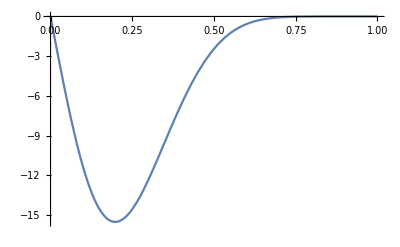

```mathematica
k =(1-r)^10*(429*r^4+450*r^3+210*r^2+50*r+5)
kernelx=FullSimplify[D[k,r]*x/r]
kernely=FullSimplify[D[k,r]*y/r]
kernelx/.{r->0.0698771,x->0.0625}
Plot[kernelx/.{x->r*Cos[θ]}/.{θ->0},{r,0,1}]
```

26 (-1+r)^8 ((-1+r) (5+3 r (15+r (53+77 r)))+132 (1+r (8+21 r)) x^2)

26 (-1+r)^8 ((-1+r) (5+3 r (15+r (53+77 r)))+132 (1+r (8+21 r)) y^2)

3432 (-1+r)^8 (1+r (8+21 r)) x y

-130.

-126.807

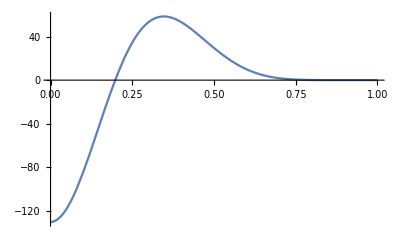

```mathematica
kernelxx =FullSimplify[D[D[k,r]/r,r]*(x/r)*x+D[k,r]/r]
kernelyy =FullSimplify[D[D[k,r]/r,r]*(y/r)*y+D[k,r]/r]
kernelxy =FullSimplify[D[D[k,r]/r,r]*(y/r)*x]
kernelyy/.{r->0.0,y->0.0}
kernelyy/.{r->0.025,y->0.025}
Plot[kernelxx/.{x->r*Cos[θ]}/.{θ->0},{r,0,1}]
```

6864 (-1+r)^6 (2+12 r-3 r^2-158 r^3+147 r^4+30 (-3+r (-18+49 r)) x^2)

6864 (-1+r)^6 (2+12 r-3 r^2-158 r^3+147 r^4+30 (-3+r (-18+49 r)) y^2)

205920 (-1+r)^6 (-3+r (-18+49 r)) x y

10259.3

11643.5

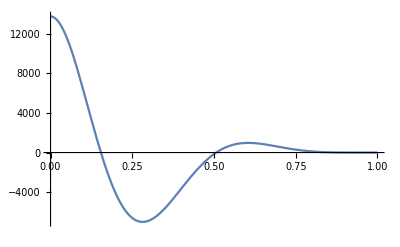

```mathematica
laplace = FullSimplify[D[D[k,r]/r,r]*(x/r)*x+D[k,r]/r]+FullSimplify[D[D[k,r]/r,r]*(y/r)*y+D[k,r]/r];
laplace=FullSimplify[laplace/.{x->r*Cos[θ],y->r*Sin[θ]}];
laplacexx=FullSimplify[D[D[laplace,r]/r,r]*(x/r)*x+D[laplace,r]/r]
laplaceyy =FullSimplify[D[D[laplace,r]/r,r]*(y/r)*y+D[laplace,r]/r]
laplacexy =FullSimplify[D[D[laplace,r]/r,r]*(y/r)*x]
laplaceyy/.{r->0.09013878189,y->-0.05}
laplaceyy/.{r->0.0790569,y->-0.025}
Plot[laplacexx/.{x->r*Cos[θ],y->r*Sin[θ]}/.{θ->0},{r,0,1}]
```

```mathematica
x
```

2471040 (-1+r)^4 (-1-4 r+46 r^2-90 r^3+49 r^4+14 (8+r (-31+28 r)) x^2)

2471040 (-1+r)^4 (-1-4 r+46 r^2-90 r^3+49 r^4+14 (8+r (-31+28 r)) y^2)

34594560 (-1+r)^4 (8+r (-31+28 r)) x y

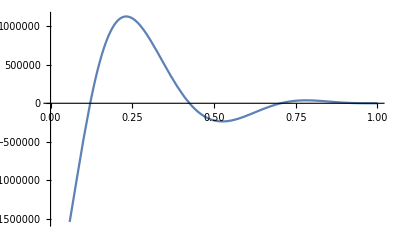

```mathematica
laplace2 = FullSimplify[D[D[laplace,r]/r,r]*(x/r)*x+D[laplace,r]/r]+FullSimplify[D[D[laplace,r]/r,r]*(y/r)*y+D[laplace,r]/r];
laplace2=FullSimplify[laplace2/.{x->r*Cos[θ],y->r*Sin[θ]}];
laplace2xx=FullSimplify[D[D[laplace2,r]/r,r]*(x/r)*x+D[laplace2,r]/r]
laplace2yy =FullSimplify[D[D[laplace2,r]/r,r]*(y/r)*y+D[laplace2,r]/r]
laplace2xy =FullSimplify[D[D[laplace2,r]/r,r]*(y/r)*x]
Plot[laplace2xx/.{x->r*Cos[θ]}/.{θ->0},{r,0,1}]
```